## Лабораторная работа №5 Крощук Виктор, ПО-5

## Задание 1

1.Пробел выполняет роль знака умножения

```mathematica
3 5 a a
```

15 a^2

2.Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3                5
```

15

```mathematica
2+   7
```

9

```mathematica
2  /3
```

2/3

3. Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
18 ^(1/2)
```

3 √2

```mathematica
3      /7
```

3/7

4.Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
18. ^(1/2)
```

4.24264

5.Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
3                   (2 +  8 )
```

30

## Задание 2

1. С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

2. Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
N[ⅇ^(Pi *Sqrt[155]), 40]
```

9.690554295137172570261414002741913992316×10^16

```mathematica
Round[%]
```

96905542951371726

3. Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

4. Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

## Задание 3

1. Решить уравнения числ прибл

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

2. Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

## Задание 4

```mathematica
Мой вариант 11
```

```mathematica
FindRoot[2*Sin[x]+1== x^2-2x-3 , {x, 4}]
```

{x→3.20675}

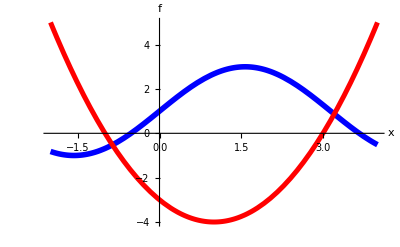

```mathematica
Plot[{2*Sin[x]+1, x^2-2x-3}, {x, -2,4}, PlotStyle->{{Thickness[0.01], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "f"}]
```

```mathematica
FindRoot[2*Sin[x]+1== x^2-2x-3, {x, -0.86}]
```

{x→-0.864917}

```mathematica
FindRoot[2*Sin[x]+1== x^2-2x-3, {x, 3.2}]
```

{x→3.20675}

## Задание 5

```mathematica
sol1=NDSolve[{y''[x]+(1+Cos[x])* y [x]==0, y[0]==0, y'[0]==1},y, {x,-4,4}]
```

{{y→InterpolatingFunction[…]}}

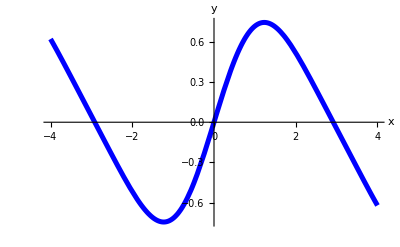

```mathematica
Plot[y[x]/.sol1, {x,-4,4}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
sol2=FindRoot[(y[x]/.sol1[[1]])==0, {x,-2.9}]
```

{x→-2.91805}

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2
```

-0.583582

```mathematica
sol3 = FindRoot[D[y[x]/.sol1[[1]],x]==0, {x,-1.2}]
```

{x→-1.23053}

```mathematica
y[x]/.sol1[[1]]/.sol3
```

-0.745676

```mathematica
FindMinimum[y[x]/.sol1[[1]], {x,-1.2}]
```

{-0.745676,{x→-1.23053}}

```mathematica
FindMaximum[y[x]/.sol1[[1]], {x,1.2}]
```

{0.745676,{x→1.23053}}

## Задание 6

```mathematica
task1 = Table[{x,(21+52x+73 x^2+17 x^3+33 x^4)(1+Random[Real, {-0.2,0.2}])}, {x,0,5,0.25}]
```

{{0.,24.1945},{0.25,44.7631},{0.5,56.79},{0.75,128.365},{1.,200.189},{1.25,351.824},{1.5,422.376},{1.75,834.259},{2.,1085.34},{2.25,1781.76},{2.5,1769.5},{2.75,3328.9},{3.,3244.21},{3.25,5628.64},{3.5,7832.46},{3.75,9629.32},{4.,10082.7},{4.25,15731.4},{4.5,17998.},{4.75,22236.5},{5.,22731.9}}

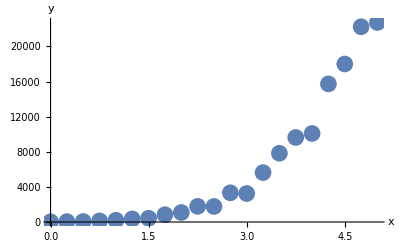

```mathematica
taskPlot=ListPlot[task1, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

```mathematica
наилучшее приближение
```

```mathematica
y3=Fit[task1, {1,x,x^2, x^3, x^4},x]
```

-325.105+2438.46 x-2663.69 x^2+1014.02 x^3-76.8614 x^4

```mathematica
y4=Fit[task1, {1,x,x^2, x^3, x^4},x]
```

-325.105+2438.46 x-2663.69 x^2+1014.02 x^3-76.8614 x^4

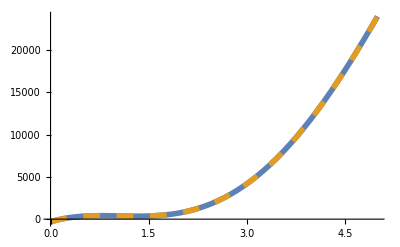

```mathematica
plot1 =Plot[{y3,y4}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

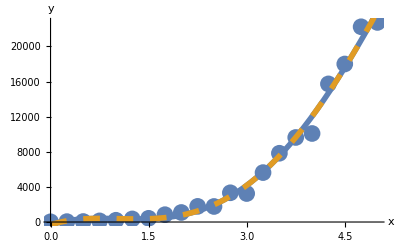

```mathematica
Show[taskPlot, plot1]
```

```mathematica
task2 = Table[{x,(21+42x+84Sin[x]+35Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,51.5689},{0.25,92.305},{0.5,116.722},{0.75,147.849},{1.,162.884},{1.25,163.379},{1.5,175.575},{1.75,165.48},{2.,170.442},{2.25,157.825},{2.5,138.568},{2.75,122.959},{3.,115.323},{3.25,102.28},{3.5,103.856},{3.75,94.9979},{4.,95.2872},{4.25,110.086},{4.5,108.497},{4.75,150.043},{5.,153.319}}

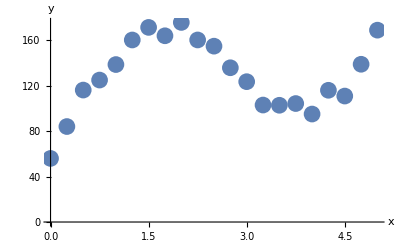

```mathematica
task2Plot=ListPlot[task2, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[task2, {1,x,Sin[x], Cos[x]},x]
```

18.4956+43.2717 x+35.5717 Cos[x]+83.7646 Sin[x]

```mathematica
y2=Fit[task2, {1,x,x^2, x^3, x^4},x]
```

48.8542+164.34 x-65.3283 x^2+4.88207 x^3+0.512335 x^4

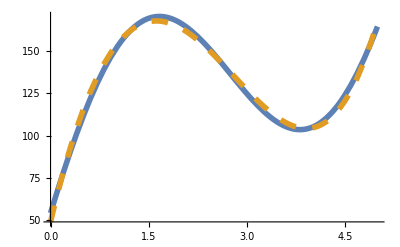

```mathematica
plot2 =Plot[{y1,y2}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

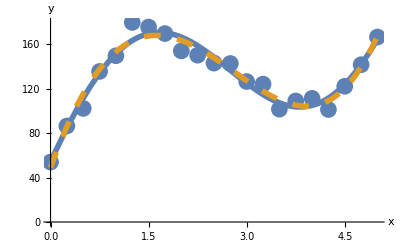

```mathematica
Show[task2Plot, plot2]
```